```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/610nm.dat"]
```

{{1.63065,0.214305},{1.58758,0.22034},{1.51023,0.233094},{1.46132,0.245218},{1.41705,0.253556},{1.38078,0.263594},{1.34407,0.270714},{1.30453,0.270256},{1.27782,0.278313},{1.24828,0.276874},{1.22646,0.280733},{1.20042,0.287432},{1.183,0.291026},{1.16401,0.288332},{1.14739,0.289306},{1.13423,0.292222},{1.12389,0.290727},{1.11401,0.101834},{1.10574,0.264669},{1.09905,0.236652},{1.09389,0.240669},{1.08918,0.279902},{1.08895,0.285104},{1.08874,0.284803},{1.08738,0.318017},{1.08767,0.315322},{1.08994,0.304465},{1.0948,0.312253},{1.10288,0.31503},{1.1168,0.325339},{1.12832,0.293639},{1.1517,0.316197},{1.18117,0.314227},{1.20042,0.307705},{1.25083,0.303728},{1.28067,0.29684},{1.3108,0.295278},{1.33715,0.291026}}

0.401958-0.101755 x

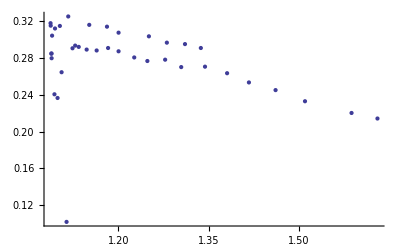

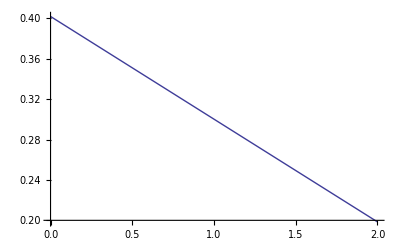

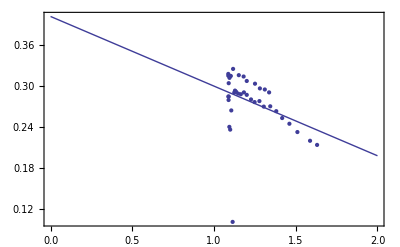

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```